```mathematica
Quit[]
```

# Electroweak baryogenesis at high wall velocities (arXiv:2001.00568)

## Master Code Reformulated

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];*)
```

```mathematica
WP=MachinePrecision;
(*******************************************************************************************************************)
(**********************************************************************************************)
```

```mathematica
(*gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];*)
gtab=Import["./satoshi_dof.dat","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
(*params3=Import["SCANS/BAU/Z2_breaking_sols_BAU_All.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc_0"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
shighlist=params3[All,"shigh"];
slowlist=params3[All,"slow"];
alphalist=params3[All,"alpha_max"];*)
```

```mathematica
params3=Import["SCANS/top_yukawa_rescaled_vw_solutions_All.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc_0"]//Normal;
TpoverTnlist=params3[All,"Tp/TN"]//Normal;
vwlist=params3[All,"vw"]//Normal;
vplist=params3[All,"vp"]//Normal;
h0list=params3[All,"h0"]//Normal;
Lhlist=params3[All,"Lh"]//Normal;
Lslist=params3[All,"Ls"]//Normal;
dslist=params3[All,"ds"]//Normal;
shighlist=params3[All,"shigh"]//Normal;
slowlist=params3[All,"slow"]//Normal;
alphalist=params3[All,"alpha_max"]//Normal;
mslist=params3[All,"ms"]//Normal;
```

```mathematica
MasterFunction[Tn_,vw_,h0_,Lh_,sl_,sh_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,sl,sh,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
(*s[z_]:=s0/2(1-Tanh[z/Ls-ds]);*)(**equation (50)**)
s[z_]:=(sl-sh)/2 Tanh[z/Ls-ds]+(sl+sh)/2;
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];
```

```mathematica
(*MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_l=",slowlist[[i]]," s_h=",shighlist[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
```

```mathematica
MasterPars[10]
```

Pars α=0.0197156 T_n=94.3245 v_w=0.659536 T_p=109.465 v_p=0.486248 h_0=204.881 L_h=0.0444972 s_l=118.712 s_h=4.77879 L_s=0.0444972 ds=0.462675

```mathematica
(*MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
(*MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];*)
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,7,points];
```

```mathematica
Import["SCANS/BAU/BAU_5.csv"]
```

MakeExpression::boxfmt: InputForm in MakeExpression[FormBox[RowBox[{Import,[,"SCANS/BAU/BAU_5.csv",]}],InputForm],InputForm] is not a box formatting type. A box formatting type is any member of $BoxForms.

```mathematica
myBAU
```

myBAU

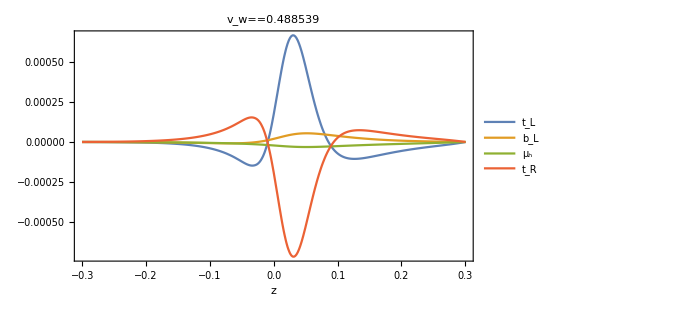
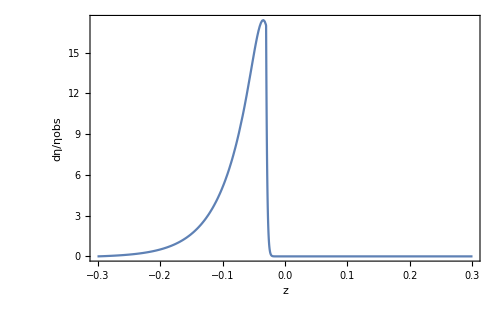
{-Graphics-,-Graphics-,1.02868}

```mathematica
MasterOutputVel[2,606.073165442302,300]
```

```mathematica
BAUscale[i_]:=Module[{BAU,res,numpoints=100},

BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,numpoints][[3]];

If[BAU[100]<1,Print[Show[MasterOutputVel[i,100,numpoints][[1]]]];Print["Did not work!!, \n Λ_CP="];Return[99]];

Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];

MasterPars[i];
Print[MasterOutputVel[i,res,numpoints][[1]]];
Print["Λ=",res];
Return[res]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Pars α=0.0187036 T_n=93.8922 v_w=0.659907 T_p=108.835 v_p=0.488539 h_0=204.479 L_h=0.0429076 s_l=117.2 s_h=4.83655 L_s=0.0429075 ds=0.497581

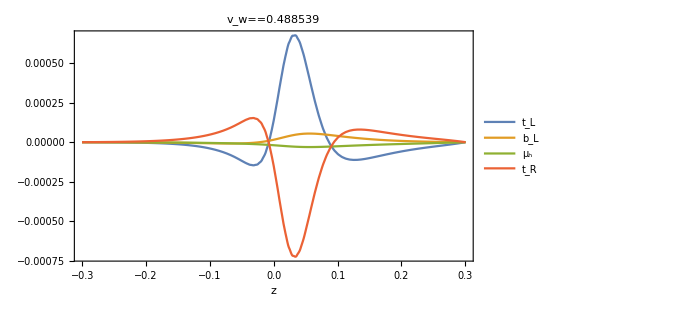

Λ=606.073

606.073

```mathematica
BAUscale[2]
```

```mathematica
BAULambda80=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["SCANS/BAU/BAU_5.csv",BAULambda80]
```

Pars α=0.019556 T =92.7586 v =0.653786 T =107.05 v =0.485561 h =207.422 L =
                 n          w           p         p           0          h
 
>   0.0474536 s =115.214 s =4.66513 L =0.0474536 ds=0.502942
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[FontColor -> GrayLevel[0], 
 
>       FontWeight -> Normal, FontSize -> 16, FontFamily -> Times, 
 
>       Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[FontColor -> GrayLevel[0], FontWeight -> Normal, 
 
>       FontSize -> 16, FontFamily -> Times, Opacity[1.], 
 
>       RGBColor[0.880722, 0.611041, 0.142051], AbsoluteThickness[1.6]], 
 
>      Directive[FontColor -> GrayLevel[0], FontWeight -> Normal, 
 
>       FontSize -> 16, FontFamily -> Times, Opacity[1.], 
 
>       RGBColor[0.560181, 0.691569, 0.194885], AbsoluteThickness[1.6]], 
 
>      Directive[FontColor -> GrayLevel[0], FontWeight -> Normal, 
 
>       FontSize -> 16, FontFamily -> Times, Opacity[1.], 
 
>       RGBColor[0.922526, 0.385626, 0.209179], AbsoluteThickness[1.6]]}, 
 
>     {t ,  b ,  μ , t }, LegendMarkers -> None, LabelStyle -> {}, 
        L    L    h   R
 
>     LegendLayout -> Column], After, Identity]]

Λ=555.341

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0161409 T =97.2718 v =0.642665 T =110.521 v =0.491654 h =202.778 L =
                  n          w           p          p           0          h
 
>   0.0469377 s =113.179 s =5.10018 L =0.0469377 ds=0.495901
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=496.42

Pars α=0.0197309 T =94.4482 v =0.661766 T =109.839 v =0.486617 h =204.694 L =
                  n          w           p          p           0          h
 
>   0.0451928 s =114.911 s =4.72449 L =0.0451928 ds=0.462378
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=568.057

Pars α=0.0154097 T =100.079 v =0.639978 T =113.291 v =0.493074 h =199.464 L =
                  n          w           p          p           0          h
 
>   0.0435987 s =116.192 s =5.4227 L =0.0435986 ds=0.433459
               l          h         s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=547.036

Pars α=0.0146885 T =101.826 v =0.64147 T =115.273 v =0.495189 h =196.73 L =
                  n          w          p          p           0         h
 
>   0.0434427 s =113.566 s =5.68048 L =0.0434427 ds=0.398795
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=525.347

Pars α=0.0150654 T =101.208 v =0.643947 T =114.91 v =0.494584 h =197.373 L =
                  n          w           p         p           0          h
 
>   0.0431133 s =116.331 s =5.67246 L =0.0431132 ds=0.402204
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=546.682

Pars α=0.0141057 T =101.784 v =0.631239 T =114.057 v =0.495178 h =197.614 L =
                  n          w           p          p           0          h
 
>   0.0426347 s =109.477 s =5.47375 L =0.0426347 ds=0.439073
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=514.838

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

InterpolatingFunction::dmval: 
   Input value {205.627} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {205.627} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {205.627} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Did not work!!, 
 Λ_CP=

Pars α=0.0167267 T =99.2346 v =0.659758 T =114.653 v =0.49306 h =196.67 L =
                  n          w           p          p          0         h
 
>   0.0390559 s =111.036 s =5.48044 L =0.0390559 ds=0.357981
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=602.433

Pars α=0.0187036 T =93.8922 v =0.659907 T =108.835 v =0.488539 h =204.479 L =
                  n          w           p          p           0          h
 
>   0.0429076 s =117.2 s =4.83655 L =0.0429075 ds=0.497581
               l        h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=606.073

Pars α=0.015203 T =100.336 v =0.641599 T =113.706 v =0.493866 h =197.785 L =
                 n          w           p          p           0          h
 
>   0.0408301 s =108.234 s =5.34356 L =0.04083 ds=0.419083
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=547.667

Pars α=0.018777 T =94.5019 v =0.659872 T =109.551 v =0.488369 h =205.391 L =
                 n          w           p          p           0          h
 
>   0.0500989 s =116.533 s =4.74726 L =0.0500989 ds=0.500776
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=488.059

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Did not work!!, 
 Λ_CP=

Pars α=0.0174084 T =97.3849 v =0.650519 T =111.679 v =0.489886 h =202.274 L =
                  n          w           p          p           0          h
 
>   0.0451975 s =121.222 s =5.15115 L =0.0451975 ds=0.451315
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=569.388

Pars α=0.0168827 T =96.62 v =0.655099 T =111.176 v =0.491908 h =201.683 L =
                  n        w           p          p           0          h
 
>   0.0434907 s =110.711 s =5.10753 L =0.0434906 ds=0.470509
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Pars α=0.0133335 T =103.043 v =0.62489 T =114.656 v =0.496388 h =196.674 L =
                  n          w          p          p           0          h
 
>   0.0433768 s =109.536 s =5.60134 L =0.0433768 ds=0.441978
               l          h          s

Λ=533.076

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=496.204

Pars α=0.0162331 T =98.2375 v =0.638744 T =111.246 v =0.490784 h =202.197 L =
                  n          w           p          p           0          h
 
>   0.0450475 s =108.953 s =5.03474 L =0.0450475 ds=0.466601
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=507.409

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0208167 T =90.3321 v =0.631001 T =102.354 v =0.478683 h =212.667 L =
                  n          w           p          p           0          h
 
>   0.0508294 s =112.059 s =4.41793 L =0.0508294 ds=0.519036
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

InterpolatingFunction::dmval: 
   Input value {193.22} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

Λ=567.936

InterpolatingFunction::dmval: 
   Input value {193.22} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {193.22} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0135688 T =101.336 v =0.630152 T =113.329 v =0.496505 h =198.072 L =
                  n          w           p          p           0          h
 
>   0.0455905 s =108.287 s =5.48569 L =0.0455904 ds=0.490875
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=454.956

Pars α=0.0132069 T =103.31 v =0.623381 T =114.774 v =0.496529 h =197.125 L =
                  n         w           p          p           0          h
 
>   0.0455229 s =106.771 s =5.5689 L =0.0455229 ds=0.44074
               l          h         s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=453.625

Pars α=0.0144067 T =101.733 v =0.635595 T =114.504 v =0.495027 h =197.204 L =
                  n          w           p          p           0          h
 
>   0.0427522 s =111.443 s =5.56235 L =0.0427522 ds=0.417105
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=525.642

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0172122 T =97.7489 v =0.651888 T =112.202 v =0.490583 h =201.336 L =
                  n          w           p          p           0          h
 
>   0.0442111 s =113.33 s =5.09706 L =0.0442111 ds=0.435321
               l         h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=542.47

Pars α=0.0190815 T =93.5309 v =0.660913 T =108.581 v =0.487879 h =205.644 L =
                  n          w           p          p           0          h
 
>   0.0461147 s =112.437 s =4.80333 L =0.0461147 ds=0.494787
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=537.494

Pars α=0.0131611 T =103.465 v =0.623094 T =114.908 v =0.49662 h =196.874 L =
                  n          w           p          p          0          h
 
>   0.0446551 s =114.814 s =5.75176 L =0.044655 ds=0.44333
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=499.926

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars α=0.0126628 T =102.65 v =0.623294 T =113.906 v =0.498105 h =197.361 L =
                  n         w           p          p           0          h
 
>   0.0471457 s =95.5361 s =192.526 L =0.0471457 ds=0.488623
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=349.905

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0162202 T =96.3713 v =0.625421 T =107.867 v =0.488655 h =205.808 L =
                  n          w           p          p           0          h
 
>   0.0492913 s =107.123 s =4.94332 L =0.0492913 ds=0.513259
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=465.452

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars α=0.0160563 T =99.4689 v =0.650192 T =113.779 v =0.493098 h =197.593 L =
                  n          w           p          p           0          h
 
>   0.0395996 s =110.439 s =5.35947 L =0.0395996 ds=0.398273
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=586.61

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.018039 T =96.8902 v =0.657827 T =111.992 v =0.489489 h =201.872 L =
                 n          w           p          p           0          h
 
>   0.0442272 s =116.281 s =5.0466 L =0.0442271 ds=0.434619
               l          h         s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=564.504

Pars α=0.0154966 T =99.8076 v =0.637986 T =112.801 v =0.492533 h =200.347 L =
                  n          w           p          p           0          h
 
>   0.0454653 s =113.08 s =5.27412 L =0.0454653 ds=0.447778
               l         h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=507.013

Pars α=0.0140301 T =100.605 v =0.631721 T =112.768 v =0.495459 h =199.973 L =
                  n          w           p          p           0          h
 
>   0.048741 s =105.745 s =5.37278 L =0.048741 ds=0.48628
              l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=412.549

Pars α=0.0147314 T =101.34 v =0.639067 T =114.484 v =0.4947 h =197.648 L =
                  n         w           p          p         0          h
 
>   0.0431378 s =112.227 s =5.54915 L =0.0431378 ds=0.413913
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=525.594

Pars α=0.0189845 T =93.992 v =0.661 T =109.109 v =0.488109 h =205.38 L =
                  n         w        p          p           0         h
 
>   0.0468367 s =119.249 s =4.83184 L =0.0468367 ds=0.490636
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=555.697

Pars α=0.0177645 T =97.1114 v =0.654887 T =111.879 v =0.4898 h =201.827 L =
                  n          w           p          p         0          h
 
>   0.0440845 s =117.947 s =5.11702 L =0.0440844 ds=0.435989
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=573.447

InterpolatingFunction::dmval: 
   Input value {209.538} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {209.538} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

InterpolatingFunction::dmval: 
   Input value {209.538} lies outside the range of data in the interpolating
     function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval
     will be suppressed during this calculation.

Pars α=0.0193772 T =93.1735 v =0.66346 T =108.473 v =0.487687 h =205.179 L =
                  n          w          p          p           0          h
 
>   0.0435636 s =115.536 s =4.81787 L =0.0435636 ds=0.491763
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=595.669

Pars α=0.0183198 T =95.4677 v =0.650244 T =109.611 v =0.487716 h =203.968 L =
                  n          w           p          p           0          h
 
>   0.0428997 s =112.5 s =4.83801 L =0.0428997 ds=0.467096
               l        h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=585.083

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.015655 T =99.7256 v =0.641531 T =113.098 v =0.492695 h =199.7 L =
                 n          w           p          p           0        h
 
>   0.0433194 s =116.365 s =5.38695 L =0.0433194 ds=0.433662
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=555.173

Pars α=0.0200807 T =93.7121 v =0.663194 T =109.185 v =0.486125 h =206.038 L =
                  n          w           p          p           0          h
 
>   0.0476842 s =128.396 s =4.77432 L =0.0476842 ds=0.50136
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=593.62

Pars α=0.0158924 T =98.9042 v =0.638107 T =111.871 v =0.491538 h =201.559 L =
                  n          w           p          p           0          h
 
>   0.0454764 s =110.155 s =5.11148 L =0.0454763 ds=0.459722
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=500.992

Pars α=0.0120783 T =105.443 v =0.619485 T =116.476 v =0.499315 h =193.81 L =
                  n          w           p          p           0         h
 
>   0.0432085 s =107.011 s =5.87733 L =0.0432085 ds=0.430391
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=474.611

Pars α=0.0162975 T =97.4488 v =0.637106 T =110.205 v =0.490356 h =202.727 L =
                  n          w           p          p           0          h
 
>   0.0424783 s =106.761 s =208.883 L =0.0424783 ds=0.483075
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=496.28

Pars α=0.0159105 T =98.4198 v =0.647256 T =112.248 v =0.492979 h =201.461 L =
                  n          w           p          p           0          h
 
>   0.0470358 s =122.798 s =5.33138 L =0.0470357 ds=0.471416
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=524.425

Pars α=0.0126887 T =104.002 v =0.619693 T =115.054 v =0.497507 h =196.025 L =
                  n          w           p          p           0          h
 
>   0.0440617 s =105.835 s =5.62651 L =0.0440617 ds=0.449024
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=463.141

Pars α=0.0197156 T =94.3245 v =0.659536 T =109.465 v =0.486248 h =204.881 L =
                  n          w           p          p           0          h
 
>   0.0444972 s =118.712 s =4.77879 L =0.0444972 ds=0.462675
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=603.777

Pars α=0.0118212 T =105.591 v =0.61096 T =115.735 v =0.498917 h =195.934 L =
                  n          w          p          p           0          h
 
>   0.0475241 s =109.825 s =5.85649 L =0.047524 ds=0.460154
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=426.695

Pars α=0.0107548 T =107.324 v =0.600977 T =116.375 v =0.501018 h =194.519 L =
                  n          w           p          p           0          h
 
>   0.0478731 s =105.714 s =5.95103 L =0.0478731 ds=0.48351
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=395.178

Pars α=0.0139501 T =101.841 v =0.626223 T =113.588 v =0.494847 h =198.968 L =
                  n          w           p          p           0          h
 
>   0.0457159 s =109.375 s =5.41955 L =0.0457158 ds=0.455077
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Pars α=0.013839 T =101.892 v =0.624553 T =113.457 v =0.494905 h =199.286 L =
                 n          w           p          p           0          h
 
>   0.0457815 s =113.264 s =5.47325 L =0.0457815 ds=0.465191
               l          h          s

Λ=470.859

Pars α=0.0112755 T =105.69 v =0.613626 T =115.961 v =0.501011 h =196.362 L =
                  n         w           p          p           0          h
 
>   0.0531936 s =106.17 s =5.88891 L =0.0531936 ds=0.489797
               l         h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=485.468

Λ=339.265

Pars α=0.0122071 T =105.185 v =0.618476 T =116.123 v =0.49878 h =194.953 L =
                  n          w           p          p          0          h
 
>   0.0449445 s =108.013 s =5.85007 L =0.0449445 ds=0.43529
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=456.621

Pars α=0.0148654 T =99.2809 v =0.622799 T =110.6 v =0.491809 h =202.752 L =
                  n          w           p        p           0          h
 
>   0.0464694 s =107.899 s =5.09555 L =0.0464694 ds=0.463002
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=483.213

Pars α=0.0165982 T =100.201 v =0.666115 T =116.443 v =0.494427 h =194.126 L =
                  n          w           p          p           0          h
 
>   0.0380596 s =114.147 s =5.90423 L =0.0380596 ds=0.311589
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=631.652

Pars α=0.0131722 T =103.912 v =0.629272 T =116.028 v =0.497499 h =195.359 L =
                  n          w           p          p           0          h
 
>   0.0439165 s =109.408 s =5.80153 L =0.0439165 ds=0.410258
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=486.245

Pars α=0.0111444 T =106.392 v =0.602405 T =115.606 v =0.499915 h =195.871 L =
                  n          w           p          p           0          h
 
>   0.0487114 s =103.964 s =5.80093 L =0.0487114 ds=0.485615
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=382.072

Pars α=0.0132149 T =102.607 v =0.618114 T =113.481 v =0.495731 h =198.95 L =
                  n          w           p          p           0         h
 
>   0.0462245 s =108.235 s =5.44993 L =0.0462245 ds=0.478078
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=451.255

Pars α=0.0123856 T =103.73 v =0.622034 T =114.912 v =0.498748 h =198.556 L =
                  n         w           p          p           0          h
 
>   0.0538553 s =111.792 s =5.67903 L =0.0538553 ds=0.493288
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=359.484

Pars α=0.0135081 T =103.325 v =0.628164 T =115.339 v =0.49638 h =197.168 L =
                  n          w           p          p          0          h
 
>   0.0468748 s =116.788 s =5.79111 L =0.0468748 ds=0.435164
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=478.687

Pars α=0.0112379 T =107.287 v =0.610197 T =117.363 v =0.500665 h =193.837 L =
                  n          w           p          p           0          h
 
>   0.0480746 s =113.865 s =6.24695 L =0.0480745 ds=0.439647
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=427.594

Pars α=0.0124525 T =103.121 v =0.610358 T =113.125 v =0.496881 h =199.835 L =
                  n          w           p          p           0          h
 
>   0.0523427 s =108.214 s =5.51031 L =0.0523427 ds=0.488591
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=375.333

Pars α=0.0144451 T =104.203 v =0.660658 T =120.024 v =0.498835 h =188.647 L =
                  n          w           p          p           0          h
 
>   0.0375087 s =117.751 s =6.96652 L =0.0375087 ds=0.249641
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=597.838

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0169646 T =96.7088 v =0.650747 T =110.846 v =0.49098 h =203.45 L =
                  n          w           p          p          0         h
 
>   0.0491754 s =114.605 s =4.99425 L =0.0491753 ds=0.488915
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=474.287

Pars α=0.0115187 T =106.43 v =0.610648 T =116.545 v =0.499828 h =195.182 L =
                  n         w           p          p           0          h
 
>   0.0485166 s =111.185 s =6.01701 L =0.0485166 ds=0.45182
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=417.815

Pars α=0.0108124 T =109.784 v =0.624827 T =121.491 v =0.504015 h =186.882 L =
                  n          w           p          p           0          h
 
>   0.0426603 s =112.442 s =7.19497 L =0.0426603 ds=0.320053
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=452.29

Pars α=0.0127688 T =102.415 v =0.620286 T =113.375 v =0.497356 h =200.744 L =
                  n          w           p          p           0          h
 
>   0.0556467 s =110.799 s =5.48715 L =0.0556467 ds=0.519192
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=342.706

Pars α=0.0149604 T =99.6121 v =0.627131 T =111.405 v =0.492228 h =202.019 L =
                  n          w           p          p           0          h
 
>   0.0464211 s =109.248 s =5.14269 L =0.0464211 ds=0.48891
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=477.642

Pars α=0.0134067 T =99.7501 v =0.566037 T =105.929 v =0.487067 h =209.125 L =
                  n          w           p          p           0          h
 
>   0.0594358 s =104.783 s =4.97559 L =0.0594358 ds=1.
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=246.655

Pars α=0.010954 T =107.523 v =0.606637 T =117.193 v =0.501109 h =193.586 L =
                 n          w           p          p           0          h
 
>   0.0472763 s =109.676 s =6.14239 L =0.0472763 ds=0.450426
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=417.99

Pars α=0.0163547 T =95.3257 v =0.566737 T =101.882 v =0.478565 h =214.386 L =
                  n          w           p          p           0          h
 
>   0.0715443 s =113.226 s =4.37299 L =0.0715443 ds=0.518003
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=352.258

Pars α=0.0125488 T =104.802 v =0.622471 T =116.182 v =0.498324 h =195.018 L =
                  n          w           p          p           0          h
 
>   0.0443088 s =113.042 s =5.95089 L =0.0443088 ds=0.426734
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=489.564

Pars α=0.0145364 T =99.3083 v =0.623125 T =110.593 v =0.492755 h =204.168 L =
                  n          w           p          p           0          h
 
>   0.0555207 s =112.754 s =5.1082 L =0.0555207 ds=0.51761
               l          h         s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=381.339

Pars α=0.0125952 T =104.119 v =0.618336 T =115.028 v =0.49759 h =196.716 L =
                  n          w           p          p          0          h
 
>   0.0455495 s =107.604 s =5.66198 L =0.0455495 ds=0.454399
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=449.528

Pars α=0.0106391 T =106.835 v =0.607713 T =116.462 v =0.502296 h =195.862 L =
                  n          w           p          p           0          h
 
>   0.0550868 s =105.631 s =6.0033 L =0.0550867 ds=0.499509
               l          h         s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=314.687

Pars α=0.0119137 T =105.809 v =0.616603 T =116.551 v =0.499415 h =194.478 L =
                  n          w           p          p           0          h
 
>   0.0455849 s =107.433 s =5.92166 L =0.0455849 ds=0.432407
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=444.326

Pars α=0.0136183 T =100.852 v =0.616242 T =111.455 v =0.49429 h =202.501 L =
                  n          w           p          p          0          h
 
>   0.0535763 s =111.065 s =5.27782 L =0.0535763 ds=0.50314
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=387.385

Pars α=0.0129094 T =104.241 v =0.622913 T =115.692 v =0.497325 h =196.917 L =
                  n          w           p          p           0          h
 
>   0.0485532 s =116.21 s =5.84727 L =0.0485532 ds=0.443922
               l         h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=448.126

Pars α=0.0217382 T =87.84 v =0.493198 T =91.4473 v =0.431557 h =224.967 L =
                  n        w           p          p           0          h
 
>   0.113467 s =114.93 s =3.6892 L =0.113467 ds=1.
              l         h         s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=181.32

Pars α=0.0121065 T =103.686 v =0.616135 T =114.216 v =0.498756 h =198.869 L =
                  n          w           p          p           0          h
 
>   0.0534954 s =108.827 s =5.65941 L =0.0534953 ds=0.508161
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=351.658

Pars α=0.0131429 T =102.988 v =0.616331 T =113.714 v =0.495681 h =199.535 L =
                  n          w           p          p           0          h
 
>   0.0490647 s =119.381 s =5.62585 L =0.0490646 ds=0.483858
               l          h          s

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Λ=458.522

SCANS/BAU/BAU_5.csv